# QNM of Schwarzschild BHs by direct integration

## Definitions of the equations

As we are in a Schwarzschild metric, we define the metric and the Regge-Wheeler equation with the associated potential,

```mathematica
Quit[]
```

```mathematica
f[r_] := 1-(2M)/r;
V = f[r]((l(l+1))/r^2-(6M)/r^3);
EQ = f[r]^2 ψ''[r]+f[r]f'[r]ψ'[r]+(ω^2-V)ψ[r]
```

(-(-(6 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r)+ω^2) ψ[r]+(2 M (1-(2 M)/r) ψ'[r])/r^2+(1-(2 M)/r)^2 ψ''[r]

## Series Solutions

## Series at the horizon

We want to solve the field equation (the Regge-Wheeler equ) in the near-horizon limit. As our boundary condition we require that we only have ingoing waves at the horizon. We use the following ansatz ,

```mathematica
ψ[r_]:=(r-2M)^(-2I ω M)h[r];
```

We write h(r) as a sum that we need to keep to order >~10 for stability.

```mathematica
ORDH = 13;
h[r_]:=Sum[hh[i] (r-2M)^i,{i,0,ORDH+5}];
```

We now sub in this expression for ψ into the Regge-Wheeler equation,

```mathematica
EQH=(-r (l+l^2-r^2 ω^2)+2 M (3+ⅈ r ω+r^2 ω^2)) h[r]+r (2 (M-2 ⅈ M r ω) h'[r]+r (-2 M+r) h''[r]);
ss = Simplify[Series[EQH,{r,2M, ORDH}]];
eqsH =Table[SeriesCoefficient[ss,i]==0,{i,0,ORDH}];
yh=Table[hh[i],{i,1,ORDH+1}];
seriesH = Simplify[Solve[eqsH, yh]][[1]];
Length[yh]
Length[eqsH]
Clear[ψ,h]
```

14

14

We’ve expanded around the horizon and found associated coefficient for each of the terms.

## Series solution at infinity

In the large distance limit we require no incoming wave as our boundary condition. This times we use the ansatz,

```mathematica
ORDINF = 14;
```

```mathematica
ψ[r_]:= Exp[I ω r] g[r];
g[r_] := Sum[ginf[i]/r^i,{i,0,ORDINF+5}];
EQINF=g''[r] f[r]^2+g'[r] f'[r]f[r]+2 I ω f[r] g'[r]-V g[r];
```

```mathematica
ss=Simplify[Series[EQINF,{r,∞,ORDINF}]];
eqsINF=Table[SeriesCoefficient[ss,i]==0,{i,2,ORDINF}];
yinf=Table[ginf[i],{i,1,ORDINF-1}];
seriesINF=Simplify[Solve[eqsINF,yinf]][[1]];
Length[yinf]
Length[eqsINF]
Clear[ψ,g]
```

13

13

## Integration

We now perform two different integrations. Firstly we integrate from the horizon to a matching point, r = rm, imposing purely ingoing wave boundary condition and secondly from infinity to the matching point while imposing no incoming waves at infinity.

We then construct a linear combination of the two solutions and fix the ration of the coefficients in order for the linear combination to be C^0 at the matching point. Note for a generic frequency the linear combination will have discontinuous derivatives. Finally we find the eigenvalues by imposing that the linear combination is C^1.

We first define the function that does the integral.

```mathematica
INT[ω0_,rm0_,l0_,EPS0_,INF0_]:=(
ruleP={AccuracyGoal->12,PrecisionGoal->12};
param={M->1,l->l0,ω->ω0,hh[0]->1,ginf[0]->1};
rh=2M/.param;
EPS=EPS0;
rinf=INF0 M/.param;
rhn=(1+EPS)rh;
(****INTEGRATION FROM THE HORIZON***)
ψgH=(r-2M)^(-2 I ω M)Sum[hh[i] (r-2M)^i,{i,0,ORDH+1}]//.Union[param,seriesH];
BCs={ψ[rhn]==ψgH/.r->rhn,ψ'[rhn]==D[ψgH,r]/.r->rhn};
EQs={((-(-(6 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r)+ω^2) ψ[r]+(2 M (1-(2 M)/r) ψ'[r])/r^2+(1-(2 M)/r)^2 ψ''[r])==0}/.param;
rm=rm0;
solH=NDSolve[Union[EQs,BCs],ψ,{r,rhn,rm},ruleP];
ψnH=ψ[r]/.solH[[1]];
ψnHp=D[ψnH,r];
(*******)
(***INTEGRATION FROM INFINITY****)
rs=r+2M Log[r/(2M)-1]/.param;(*tortoise coordinate*)
ψgINF=Exp[I ω rs]Sum[ginf[i]/r^i,{i,0,ORDINF-1}]//.Union[param,seriesINF];
BCs={ψ[rinf]==ψgINF/.r->rinf,ψ'[rinf]==D[ψgINF,r]/.r->rinf};
EQs={((-(-(6 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r)+ω^2) ψ[r]+(2 M (1-(2 M)/r) ψ'[r])/r^2+(1-(2 M)/r)^2 ψ''[r])==0}/.param;
rm=rm0;
solINF=NDSolve[Union[EQs,BCs],ψ,{r,rinf,rm},ruleP];
ψnINF=ψ[r]/.solINF[[1]];
ψnINFp=D[ψnINF,r];
(*******)
b=ψnH/ψnINF/.r->rm;(*we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm*)
ψn=Piecewise[{{ψnH,r<rm},{b ψnINF,r≥rm}}];
Δψp=(D[ψnH,r]-D[b ψnINF,r])/D[ψnH,r]/.r->rm;
{Δψp}(*the function INT returns the jump of the first derivative at the matching point for a given ω*)
);
```

We can use the above code to find the QNM. Note that ψ is continuous, but the derivative isn’t at the matching point.

{1.86909+0.0777312 ⅈ}

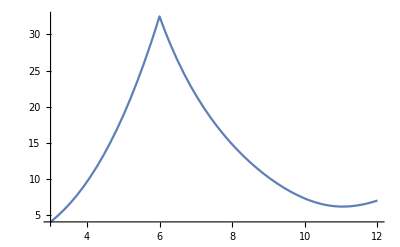

```mathematica
INT[0.1-0.1I,6,2,10^-4,10^2]
Plot[Abs[ψn],{r,0.5 rm,2 rm}]
```

## Root Finder

For ω to be  a QNM then the first derivative at the matching point must equal zero, this is equivalent to the Wronskian being equal to zero.

### Fundamental mode for l =2

```mathematica
ωguess = 0.4 - 0.1ⅈ;
f4[y_?NumericQ]:=INT[y,6,2,10^-4,3 10^1][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}][[1]];
check = Abs[f4[y0n]];
{y0n, check}
```

{0.373672-0.0889623 ⅈ,3.40125×10^-11}

Note that we can show that the solution doesn’t depend on the matching point.

```mathematica
ωguess=0.4-0.1 ⅈ;
f4[y_?NumericQ]:=INT[y,5,2,10^-4,3 10^1][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}][[1]];
check=Abs[f4[y0n]];
{y0n,check}
(****)
f4[y_?NumericQ]:=INT[y,6,2,10^-4,3 10^1][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}][[1]];
check=Abs[f4[y0n]];
{y0n,check}
(****)
f4[y_?NumericQ]:=INT[y,7,2,10^-4,3 10^1][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}][[1]];
check=Abs[f4[y0n]];
{y0n,check}
```

{0.373672-0.0889623 ⅈ,1.50388×10^-11}

{0.373672-0.0889623 ⅈ,3.40125×10^-11}

{0.373672-0.0889623 ⅈ,3.71472×10^-11}

As such we usually pick the matching point to be 3 r_schwar as this is where the function in maximum. We can also find overtones for the l=2 mode,

```mathematica
ωguess=0.35-0.2 ⅈ;
f4[y_?NumericQ]:=INT[y,6,2,10^-4,2 10^1][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}][[1]];
check=Abs[f4[y0n]];
{y0n,check}
```

{0.347923-0.274791 ⅈ,6.06575×10^-10}

## Finding the Overtones

Now that we know the code is working we want to check that we can calculate the higher overtones. For our initial guess we will read in the values calculated in the data file we are comparing to and then add a random number to insure we do in fact find the correct data. We first import the data,

```mathematica
initalGuess = Import["C:\\Users\\user\\Documents\\physics\\QNM and modifed Gravity\\s2l2.dat.csv"];
initalGuess[[1]]
numbOvertones = 20 ;(**Length[initalGuess];**)
```

{0.747343,0.177925,1.692×10^-13,0}

Next we write one really big for loop

```mathematica
predictedModes = Array[0,{numbOvertones,4}];
```

```mathematica
For[i=1, i<numbOvertones,i++,
f4[y_?NumericQ]:=INT[y,6,2,10^-4,2 10^1][[1]];
y0n=y/.FindRoot[f4[y],{y,(0.5*initalGuess[[i,1]] - 0.5*initalGuess[[i,2]]ⅈ)}, AccuracyGoal->11][[1]];
check = Abs[f4[y0n]];
predictedModes[[i]]={Re[y0n], -Im[y0n],check, i-1} ];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

NDSolve::ndsz: At r == 3.27667, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At r == 4.62553, step size is effectively zero; singularity or stiff system suspected.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {y} = {-2.89877+30.5994 ⅈ}.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {y} = {-4.14893+32.8074 ⅈ}.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {y} = {-5.3203+34.9667 ⅈ}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

```mathematica
predictedModes
```

{{0.373671,0.0889627,4.3636×10^-11,0},{0.347923,0.274791,6.53981×10^-10,1},{0.293955,0.451503,0.0180708,2},{0.502221,1.40949,0.435157,3},{0[5,1],0[5,2],0[5,3],0[5,4]}}